```mathematica
(*Use after understanding the demo, in order to use it correctly*)
```

Demo1 Visualization

```mathematica
Needs["StatisticalPlots`"]
Data={5408,5431,5475,5442,5376,5457,5407,5469,5416,5377,5444,5466, 5399,5391,5477,5427,5421,5396,5381,5425,5406,5342,5452,5420,5458,5422,5448,5366,5430,5418,5388,5459,5422,5416,5435,5420,5429,5401,5446,5487,5416,5382,5357,5388,5454,5375,5409,5459,5445,5429,5463,5408,5481,5453,5422,5354,5421,5406,5447,5329,5473,5423,5441,5412,5384,5445,5436,5454,5453,5428,5418,5465,5388,5388,5378,5481,5387,5440,5482,5406,5401,5411,5399,5431,5440,5413,5485,5431,5416,5431,5390,5399,5435,5387,5462,5383,5401,5407,5385,5440};
mean = Mean[Data]
variance = Variance[Data]
```

542177/100

11067971/9900

Histogram

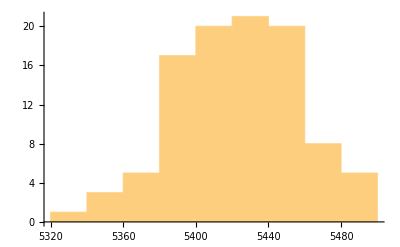

```mathematica
Histogram[Data,"FreedmanDiaconis"]
Histogram[Data,"Sturges"];
(*mma may not obey exactly the method we learn in class*)
(*For exam draw histograms using pens and can use mma for checking*)
```

StemLeafPlot

```mathematica
StemLeafPlot[Data,StemExponent->1, IncludeStemCounts->True, IncludeEmptyStems->True]
```

Stem | Leaves | Counts
532 | 9 | 1
533 |  | 0
534 | 2 | 1
535 | 47 | 2
536 | 6 | 1
537 | 5678 | 4
538 | 12345778888 | 11
539 | 016999 | 6
540 | 11166677889 | 11
541 | 123666688 | 9
542 | 0011222357899 | 13
543 | 01111556 | 8
544 | 00012455678 | 11
545 | 233447899 | 9
546 | 23569 | 5
547 | 357 | 3
548 | 11257 | 5
Stem units: 10

BoxWhiskerChart

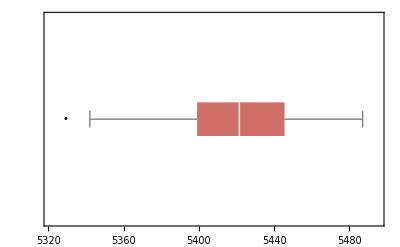

```mathematica
BoxWhiskerChart[Data,"Outliers",BarOrigin->Left,ChartStyle->56]
```

Sample Template 1

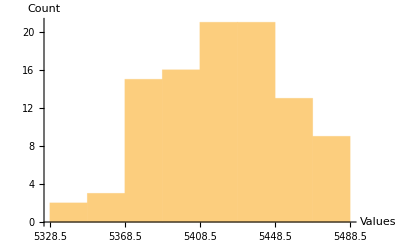

```mathematica
kSturges=Ceiling[Log2[Length[Data]]]+1;
hSturges=Ceiling[(Max[Data]-Min[Data])/kSturges];
hFreedmanDiaconis=Ceiling[(2×InterquartileRange[Data])/CubeRoot[Length[Data]]];
bins=Table[Min[Data]-0.5+i×hSturges,{i,0,kSturges}];
Histogram[Data,{Min[bins],Max[bins],hSturges},Ticks->{bins,Automatic},AxesLabel->{Values,Count}]
```

Sample Template 2

4

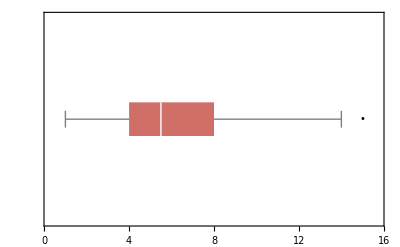

```mathematica
data = {2,2,3,7,9,14,1,4,6,4,15,3,10,4,9,4,7,3,3,12,7,5,4,7,5,3,8,6,12,7,8,5,4,6};
{q1,q2,q3}=Quartiles[data];
iqr = InterquartileRange[data];
f1 = q1-1.5*iqr;
f2 = q3+1.5*iqr;
F1 = q1-3*iqr;
F2 = q3+3*iqr;
BoxWhiskerChart[data,"Outliers",BarOrigin->Left,ChartStyle->56]
(*command with ';' not output*)
(*you can choose to design templates for chech and help in exam*)
```